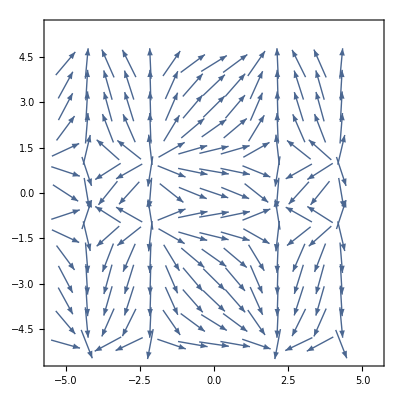

-Graphics3D-

-Graphics3D-

```mathematica
Needs["NumericalCalculus`"]
Clear[x,y,div]
f[x_,y_]=Normalize[{.5+Cos[x],Sign[y](.5-Cos[y])}];
VectorPlot[f[x,y],{x,-5,5},{y,-5,5}]
angle[x_,y_]=Max[ArcTan[x,y],ArcTan[-x,-y]];

Plot3D[angle[x,y],{x,-1,1},{y,-1,1}]
Plot3D[angle@@f[x,y],{x,-5,5},{y,-5,5},AxesLabel->Automatic,MaxRecursion->8]
div[x0_,y0_]:=ND[angle@@f[x,y0],x,x0]^2+ND[angle@@f[x0,y],y,y0]^2;
(*pts=Flatten[Table[{a,b,div[a,b]},{a,-1,1,.01},{b,-1,1,.01}],1];
ListPlot3D[pts,PlotRange->All]*)
```

```mathematica
TrigExpand@ArcTan[Cos[t],Sin[t]]
```

ArcTan[Cos[t],Sin[t]]

```mathematica
EmbeddedHTML["<iframe src=\"https://alankoval.com/3dgrapher/src/index.html?f0=z%3D~'sin~.x%2B~'sin~.y&da0=x~.y~.z~in~l%5B-10~.10~r%5D&op0=s&q0=120&t0=1&s0=150&c0=101048169&r=-086-0170476042302640866\" width='800' height='800'><p>Your browser does not support iframe</p></iframe>"]
```

Null<iframe src="https://alankoval.com/3dgrapher/src/index.html?f0=z%3D~'sin~.x%2B~'sin~.y&da0=x~.y~.z~in~l%5B-10~.10~r%5D&op0=s&q0=120&t0=1&s0=150&c0=101048169&r=-086-0170476042302640866" width='800' height='800'><p>Your browser does not support iframe</p></iframe><iframe src="https://alankoval.com/3dgrapher/src/index.html?f0=z%3D~'sin~.x%2B~'sin~.y&da0=x~.y~.z~in~l%5B-10~.10~r%5D&op0=s&q0=120&t0=1&s0=150&c0=101048169&r=-086-0170476042302640866" width='800' height='800'><p>Your browser does not support iframe</p></iframe>